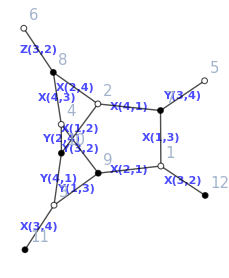

```mathematica
(*SPECIFY WHICH EXAMPLE IT IS*)
ii=49;

(*Below this you don't need to touch*)
Subscript[bft, ii];
a=a/.formatrule;
b=b/.formatrule;
c=c/.formatrule;
d=d/.formatrule;
topleft=a;
topright=b;
bottomleft=c;
bottomright=d;
viewGraph[a,b,c,d]
```

```mathematica
(*This is to fix the makeLoopVariablesBasis function*)
```

```mathematica
externaledges=Variables[Join[bottomleft,topright]];
boundaries=Gather[externaledges,Intersection[List@@#1,List@@#2]=!={}&];
(*The Gather function doesn't work recursively, so we must Gather edges into boundaries until there is nothing left to gather*)
oldexpression=Null;
While[oldexpression=!=boundaries,
oldexpression=boundaries;
boundaries=Map[Flatten,Gather[boundaries,Intersection[Flatten[Map[List@@#&,#1]],Flatten[Map[List@@#&,#2]]]=!={}&]];
];
(*Now we have the boundaries*)
bpathendpoints=Map[#[[1]]&,boundaries];
bpaths=Table[{bpathendpoints[[iii]],bpathendpoints[[iii+1]]},{iii,Length[bpathendpoints]-1}];
(*For now bpaths only contain the external edges. We'll now look for the shortest path between these edges, to complete the paths between boundaries*)
adjacencymat=getAdjacencyMatrix[topleft,topright,bottomleft,bottomright];
graph=AdjacencyGraph[adjacencymat];
externaledgestonodenumbers=MapThread[Rule,{Flatten[DeleteCases[Join[bottomleft,Transpose[topright]],0,{2}]],Join[Range[Length[bottomleft]]+Length[topleft],Range[Dimensions[topright][[2]]]+Total[Dimensions[topleft]]+Length[bottomleft]]}];
bpaths=Map[Table[UndirectedEdge[#[[iii]],#[[iii+1]]],{iii,Length[#]-1}]&,Map[FindShortestPath[graph,Sequence@@#]&,bpaths/.externaledgestonodenumbers]];
(*Now each boundary path is expressed as a list of directed edges that go from one boundary to the next. We need to turn these directed edges into a product of edges*)
kasteleyn=joinupKasteleyn[topleft,topright,bottomleft,bottomright];
bigkasteleyn=Join[kasteleyn,Transpose[kasteleyn]];
nameUndirectedEdges=Function[{undirectededge},
Block[{edgename,edgeweight},
edgename=(Intersection@@Map[Variables[bigkasteleyn[[#]]]&,List@@undirectededge])[[1]];
If[undirectededge[[1]]<undirectededge[[2]],
edgeweight=edgename;
,edgeweight=1/edgename;
];
edgeweight]
];
bpaths=Map[Times@@#&,Map[nameUndirectedEdges,bpaths,{2}]];
(*Now we have the paths running between different boundaries, expressed as products of edge variables*)
(*We shall now make all internal paths. These contain all internal faces, non-trivial paths around higher-genus, and products of external faces around each boundary*)
(*We start from a direct graph, as this will allow us to understand the direction of our internal loops*)
directedgraph=AdjacencyGraph[UpperTriangularize[adjacencymat]];
nameDirectedEdges=Function[{directededge},
Block[{edgename},
edgename=(Intersection@@Map[Variables[bigkasteleyn[[#]]]&,List@@directededge])[[1]];
bigkasteleyn=bigkasteleyn/.{edgename->0};
edgename]
];
edgelist=Map[nameDirectedEdges,EdgeList[directedgraph]];(*watch out! I have now changed bigkasteleyn! If you need it again, you'll need to reset it*)
internalpaths=Map[Times@@Power[edgelist,#]&,Normal[EdgeCycleMatrix[directedgraph]]];
(*The only paths that I still need are some external face variables: around each boundary, I only need to report all but one external faces belonging to that boundary. Then we will have completed our path basis.*)
alledges=Variables[kasteleyn];
boundaryfaces=Map[Union[Flatten[#]]&,Map[List@@#&,boundaries,{2}]];(*these are the face names around each boundary*)
missingexternalfaces=Flatten[Map[#[[Range[Length[#]-1]]]&,Map[(Times@@Cases[alledges,_[_,#]])/(Times@@Cases[alledges,_[#,_]])&,boundaryfaces,{2}]]];
loopvariablebasis=Join[{internalpaths},{missingexternalfaces},{bpaths}];

loopvariablebasis
```

{{(X[2,4] Y[2,4])/(X[1,2] X[4,3]),(X[1,3] X[2,4] Y[3,2])/(X[2,1] X[4,1] X[4,3]),(X[2,1] X[4,1] Y[4,1])/(X[1,2] X[1,3] Y[1,3])},{(X[1,2] X[3,2] Y[3,2] Z[3,2])/(X[2,1] X[2,4] Y[2,4]),(X[1,3] X[4,3] Y[1,3])/(X[3,2] X[3,4] Y[3,2] Y[3,4] Z[3,2])},{}}

```mathematica
kasteleyn=joinupKasteleyn[topleft,topright,bottomleft,bottomright];
alledges=Variables[kasteleyn];

adjacencymat=getAdjacencyMatrix[topleft,topright,bottomleft,bottomright];
directedgraph=AdjacencyGraph[UpperTriangularize[adjacencymat]];
internalpathvectors=Normal[EdgeCycleMatrix[directedgraph]]
internalpaths=Map[Times@@Power[edgelist,#]&,internalpathvectors];
tosolvefor=Total[Table[coef[iii]internalpathvectors[[iii]],{iii,Length[internalpathvectors]}]];
coeflist=Table[coef[iii],{iii,Length[internalpathvectors]}];

facevariables=Map[(Times@@Cases[alledges,_[_,#]])/(Times@@Cases[alledges,_[#,_]])&,allFaceLabels[topleft,topright,bottomleft,bottomright]];
facevariablevectors=Map[Table[D[#,alledges[[iii]]],{iii,Length[alledges]}]/.Map[#->1&,alledges]&,facevariables]
Map[Solve[tosolvefor==#,coeflist]&,facevariablevectors]
```

{{0,0,0,0,1,-1,0,0,0,-1,0,1,0,0},{1,-1,0,-1,1,0,0,0,0,-1,1,0,0,0},{-1,1,0,1,0,-1,-1,1,0,0,0,0,0,0}}

{{-1,-1,1,0,0,0,1,0,-1,0,0,0,1,0},{1,0,-1,-1,1,0,0,0,0,-1,1,0,0,1},{0,1,0,0,-1,-1,0,1,1,0,-1,-1,0,-1},{0,0,0,1,0,1,-1,-1,0,1,0,1,-1,0}}

{{},{},{},{}}

```mathematica
bpaths=Subsets[externaledges,{2}]

externaledgestonodenumbers=MapThread[Rule,{Flatten[DeleteCases[Join[bottomleft,Transpose[topright]],0,{2}]],Join[Range[Length[bottomleft]]+Length[topleft],Range[Dimensions[topright][[2]]]+Total[Dimensions[topleft]]+Length[bottomleft]]}];
bpaths=Map[Table[UndirectedEdge[#[[iii]],#[[iii+1]]],{iii,Length[#]-1}]&,Map[FindShortestPath[graph,Sequence@@#]&,bpaths/.externaledgestonodenumbers]];
kasteleyn=joinupKasteleyn[topleft,topright,bottomleft,bottomright];
bigkasteleyn=Join[kasteleyn,Transpose[kasteleyn]];
nameUndirectedEdges=Function[{undirectededge},
Block[{edgename,edgeweight},
edgename=(Intersection@@Map[Variables[bigkasteleyn[[#]]]&,List@@undirectededge])[[1]];
If[undirectededge[[1]]<undirectededge[[2]],
edgeweight=edgename;
,edgeweight=1/edgename;
];
edgeweight]
];
bpaths=Map[Times@@#&,Map[nameUndirectedEdges,bpaths,{2}]]

basisvectors=Map[Table[D[#,alledges[[iii]]],{iii,Length[alledges]}]/.Map[#->1&,alledges]&,bpaths]

facenames=Union[Flatten[Map[List@@#&,alledges]]];
facevariables=Map[(Times@@Cases[alledges,_[_,#]])/(Times@@Cases[alledges,_[#,_]])&,facenames];
(*We'll now need to see whichof the internalpaths are simply products of internal faces, and which ones wrap non-trivial cycles around a higher-genus surface*)
facevariablevectors=Map[Table[D[#,alledges[[iii]]],{iii,Length[alledges]}]/.Map[#->1&,alledges]&,facevariables];
tosolvefor=Total[Table[coef[iii]facevariablevectors[[iii]],{iii,Length[facevariablevectors]-1}]];
coeflist=Table[coef[iii],{iii,Length[facevariablevectors]-1}];

Map[Solve[tosolvefor==#,coeflist]&,basisvectors]
```

{{X[3,2],X[3,4]},{X[3,2],Y[3,4]},{X[3,2],Z[3,2]},{X[3,4],Y[3,4]},{X[3,4],Z[3,2]},{Y[3,4],Z[3,2]}}

{(X[2,1] X[3,4])/(X[3,2] Y[1,3]),X[1,3]/(X[3,2] Y[3,4]),(X[1,3] X[2,4])/(X[3,2] X[4,1] Z[3,2]),(X[1,3] Y[1,3])/(X[2,1] X[3,4] Y[3,4]),(X[4,3] Y[1,3])/(X[3,4] Y[3,2] Z[3,2]),(X[2,4] Y[3,4])/(X[4,1] Z[3,2])}

{{0,0,1,0,-1,1,0,0,-1,0,0,0,0,0},{0,1,0,0,-1,0,0,0,0,0,0,-1,0,0},{0,1,0,1,-1,0,-1,0,0,0,0,0,0,-1},{0,1,-1,0,0,-1,0,0,1,0,0,-1,0,0},{0,0,0,0,0,-1,0,1,1,0,-1,0,0,-1},{0,0,0,1,0,0,-1,0,0,0,0,1,0,-1}}

{{},{},{},{},{},{}}

```mathematica
(*We'll change basis such that we only have the nontrivial cycles around high-genus surfaces, face variables,and paths stretching between different boundaries*)
(*We'll start by making all the face variables*)
facenames=Union[Flatten[Map[List@@#&,alledges]]];
facevariables=Map[(Times@@Cases[alledges,_[_,#]])/(Times@@Cases[alledges,_[#,_]])&,facenames];
(*We'll now need to see whichof the internalpaths are simply products of internal faces, and which ones wrap non-trivial cycles around a higher-genus surface*)
facevariablevectors=Map[Table[D[#,alledges[[iii]]],{iii,Length[alledges]}]/.Map[#->1&,alledges]&,facevariables];
tosolvefor=Total[Table[coef[iii]facevariablevectors[[iii]],{iii,Length[facevariablevectors]-1}]];
coeflist=Table[coef[iii],{iii,Length[facevariablevectors]-1}];
(*Let's turn the internalpaths into vectors*)
basisvectors=Map[Table[D[#,alledges[[iii]]],{iii,Length[alledges]}]/.Map[#->1&,alledges]&,internalpaths];
(*These are the paths in our basis that are not purely expressibly in terms of faces*)
nontrivialpaths=Cases[basisvectors,zz_/;Length[Solve[tosolvefor==zz,coeflist]]==0];
(*We'll now add independent non-trivial cycles (in vector form) to a list called genuspaths*)
genuspaths={};
accountedforvectors=facevariablevectors;
While[nontrivialpaths=!={},
genuspaths=Append[genuspaths,nontrivialpaths[[1]]];
accountedforvectors=Prepend[accountedforvectors,nontrivialpaths[[1]]];
tosolvefor=tosolvefor+accountedforvectors[[1]]coef[Length[accountedforvectors]-1];
coeflist=Append[coeflist,coef[Length[accountedforvectors]-1]];
nontrivialpaths=Cases[nontrivialpaths,zz_/;Length[Solve[tosolvefor==zz,coeflist]]==0];
];
(*We now have all paths wrapping non-trivial cycles on the higher-genus surface. Turn these into products of edges*)
genuspaths=Map[Times@@Power[alledges,#]&,genuspaths];
(*We'll split the internal faces from the external ones*)
internalfacevariables=facevariables[[Flatten[Position[facenames,Alternatives@@internalFaceLabels[topleft,topright,bottomleft,bottomright]]]]];
externalfacevariables=Complement[facevariables,internalfacevariables];
(*We now remove one face from the total, since they are not all independent. If we only have internal faces, remove one of those. Otherwise remove an external face*)
```

```mathematica
(*This is to fix the moduliLoopVariablesBFT function*)
```

```mathematica
moduliSpaceBFT[a,b,c,d,2]
```

{{0,0,0,1,0,1,0,0,1,0,1,0,1,1},{0,0,1,0,1,0,0,0,0,1,0,1,1,0},{0,0,1,1,1,1,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1,1,1,1,1}}

```mathematica
referencematching=Null;
loopvariablebasis=Null;
gauging=2;

perfmatchings=perfectMatchings[topleft,topright,bottomleft,bottomright];
If[referencematching===Null,
referenceperfmatch=perfmatchings[[1]];
,referenceperfmatch=referencematching;
];
If[loopvariablebasis===Null,
(*make my own basis*)
If[gauging==2,
basispaths=makeLoopVariablesBasis[topleft,topright,bottomleft,bottomright];
,basispaths=makeLoopVariablesBasis[topleft,topright,bottomleft,bottomright,True];
];
,basispaths=loopvariablebasis;
];
(*The first part contains the internal loops, the second contains remaining external faces, and the final contains paths strecthing between different boundaries*)
basis=Flatten[basispaths];
(*We'll now express each perfect matching as a vector describing which edges are present (1: in numerator; -1: in denominator; 0: absent)*)
kasteleyn=joinupKasteleyn[topleft,topright,bottomleft,bottomright];
allvariables=Variables[kasteleyn];
perfmatchingvectors=Map[Table[D[#,allvariables[[iii]]],{iii,Length[allvariables]}]/.Map[#->1&,allvariables]&,perfmatchings/referenceperfmatch];
(*We'll also express the path basis in this vectorial way*)
basisvectors=Map[Table[D[#,allvariables[[iii]]],{iii,Length[allvariables]}]/.Map[#->1&,allvariables]&,basis];
(*We can now solve for which basis vectors are required to form a given expression*)
tosolvefor=Total[Table[coef[iii]basisvectors[[iii]],{iii,Length[basisvectors]}]];coeflist=Table[coef[iii],{iii,Length[basisvectors]}];
perfmatchingsasloops=Map[#[[2]]&,Map[Solve[tosolvefor==#,coeflist][[1]]&,perfmatchingvectors],{2}];
(*We now have the expression of each perfect matching in terms of the loop basis*)
masterspace=Transpose[perfmatchingsasloops];
(*We need to gauge away all internal faces, and if we use gauging 2 also all internal loops. This corresponds to the first rows of the masterspace*)
If[loopvariablebasis===Null,
(*if I made my own basis, I arranged it such that the first entry is what we'll be gauging away. Otherwise, we'll need to find what to gauge away by hand*)
modulispace=masterspace[[Range[Length[basispaths[[1]]]+1,Length[basis]]]];
,(*We need to gauge away internal faces only. We'll find out how to express internal faces in terms of basispaths, and then mod out by these expressions*)
internalfacenames=internalFaceLabels[topleft,topright,bottomleft,bottomright];
internalfacevariables=Map[(Times@@Cases[allvariables,_[_,#]])/(Times@@Cases[allvariables,_[#,_]])&,internalfacenames];
internalfacevariablevectors=Map[Table[D[#,allvariables[[iii]]],{iii,Length[allvariables]}]/.Map[#->1&,allvariables]&,internalfacevariables];
tosolvefor=Total[Table[coef[iii]basisvectors[[iii]],{iii,Length[basisvectors]}]];
coeflist=Table[coef[iii],{iii,Length[basisvectors]}];
(*We'll now express the internal faces as a combination of basis paths*)
internalfacesasbasispaths=Map[#[[2]]&,Map[Solve[tosolvefor==#,coeflist][[1]]&,internalfacevariablevectors],{2}];
(*We'll need to mod out by these vectors, as they represent internal faces*)
vectorMod=Function[{vector,modoutbyvectors},
Total[Map[Projection[vector,#]&,NullSpace[modoutbyvectors]]]
];
modulispace=Transpose[Map[vectorMod[#,internalfacesasbasispaths]&,perfmatchingsasloops]];
];
{masterspace,modulispace,basis}
```

```mathematica
(*This is to fix the getGrassmannian function*)
```

```mathematica
(*This is a planar example*)
```

```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
aa={{Subscript[X, 1,7](*+Subscript[X, 7,7]*),Subscript[X, 2,1](*+Subscript[X, 2,100]*),Subscript[X, 3,2](*+Subscript[X, 2,1]*)(*+Subscript[Z, 30]*),Subscript[X, 8,3](*+Subscript[X, 8,3]*),0,0,0},{Subscript[X, 13,1],Subscript[X, 1,4],0,0,Subscript[X, 4,13],0,0},{0,Subscript[X, 4,2],Subscript[X, 2,5],0,0,Subscript[X, 5,4],0},{0,0,Subscript[X, 5,3],Subscript[X, 3,6],0,0,Subscript[X, 6,5]},{0,0,0,0,Subscript[X, 12,4],Subscript[X, 4,11],0},{0,0,0,0,0,Subscript[X, 11,5],Subscript[X, 5,10]},{0,0,0,Subscript[X, 6,9],0,0,Subscript[X, 10,6]}}/.formatrule;
bb={{0,0,0,Subscript[X, 7,8]},{0,0,0,0},{0,0,0,0},{0,0,0,0},{Subscript[X, 11,12],0,0,0},{0,Subscript[X, 10,11],0,0},{0,0,Subscript[X, 9,10],0}}/.formatrule;
cc={{Subscript[X, 7,13],0,0,0,0,0,0},{0,0,0,Subscript[X, 9,8],0,0,0},{0,0,0,0,Subscript[X, 13,12],0,0}}/.formatrule;
dd={{0,0,0,0},{0,0,0,0},{0,0,0,0}}/.formatrule;

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
(*This is a non-planar example with secret poles*)
```

```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
aa={{Subscript[X, 8,1],Subscript[X, 1,7](*+Subscript[X, 1,700]*),0,0,0,0},{0,Subscript[X, 2,1](*+Subscript[X, 2,100]*),0,0,Subscript[X, 4,2],Subscript[X, 1,4]},{Subscript[X, 1,9],0,Subscript[X, 9,3],Subscript[X, 3,6],0,Subscript[X, 6,1]},{0,Subscript[X, 7,2],Subscript[X, 3,7],Subscript[X, 2,3],0,0},{0,0,0,Subscript[X, 6,2],Subscript[X, 2,5],0}}/.formatrule;
bb={{Subscript[X, 7,8],0},{0,0},{0,0},{0,0},{0,Subscript[X, 5,6]}}/.formatrule;
cc={{Subscript[X, 9,8],0,0,0,0,0},{0,0,Subscript[X, 7,9],0,0,0},{0,0,0,0,0,Subscript[X, 4,6]},{0,0,0,0,Subscript[X, 5,4],0}}/.formatrule;
dd={{0,0},{0,0},{0,0},{0,0}}/.formatrule;

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
(*This is another non-planar example with secret poles*)
```

```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
aa={{Subscript[X, 3,9],0,Subscript[X, 6,3],0},{Subscript[X, 8,3],Subscript[X, 2,8],0,Subscript[X, 3,2]},{0,Subscript[X, 7,1],Subscript[X, 1,6],0},{0,Subscript[X, 1,2],Subscript[X, 5,1],Subscript[X, 2,4]},{0,0,Subscript[X, 3,5],Subscript[X, 4,3]}}/.formatrule;
bb={{Subscript[X, 9,6],0,0,0},{0,0,0,0},{0,Subscript[X, 6,7],0,0},{0,0,0,Subscript[X, 4,5]},{0,0,Subscript[X, 5,4],0}}/.formatrule;
cc={{Subscript[X, 9,8],0,0,0},{0,Subscript[X, 8,7],0,0}}/.formatrule;
dd={{0,0,0,0},{0,0,0,0}}/.formatrule;

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
(*This is a non-planar example without secret poles*)
```

```mathematica
{aa,bb,cc,dd}={{{Subscript[Z, 10],Subscript[Z, 1],0,Subscript[Z, 7],0},{0,Subscript[Z, 12],Subscript[Z, 2],0,0},{0,Subscript[Z, 14],Subscript[Z, 15],0,Subscript[Z, 4]},{0,0,Subscript[Z, 16],Subscript[Z, 3],0},{Subscript[Z, 9],Subscript[Z, 18],0,0,Subscript[Z, 19]}},{{0,0,0},{Subscript[Z, 13],0,0},{0,0,0},{0,Subscript[Z, 17],0},{0,0,Subscript[Z, 5]}},{{Subscript[Z, 21],0,0,0,0},{0,0,0,Subscript[Z, 8],0},{0,0,0,0,Subscript[Z, 6]}},{{0,0,0},{0,0,0},{0,0,0}}}/.{Subscript[XX_, z1_]->XX[z1]};

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
(*This is the planar double square box*)
```

```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
aa={{Subscript[X, 3,1],Subscript[X, 1,2],Subscript[X, 2,3]},{Subscript[X, 1,4],Subscript[X, 5,1],0},{0,Subscript[X, 2,5],Subscript[X, 6,2]}}/.formatrule;
bb={{0,0},{0,Subscript[X, 4,5]},{Subscript[X, 5,6],0}}/.formatrule;
cc={{0,0,Subscript[X, 3,6]},{Subscript[X, 4,3],0,0}}/.formatrule;
dd={{0,0},{0,0}}/.formatrule;

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
(*Has 3 boundaries, but is reducible. It's a top cell of Gr(3,5). It's a 'reduction' of the monster guy below.*)
```

```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
aa={{Subscript[X, 7,1],Subscript[X, 1,6],0,0,0},{Subscript[X, 1,3],Subscript[X, 3,1],0,0,0},{Subscript[X, 3,7],0,Subscript[X, 4,3],Subscript[X, 7,4],0},{0,Subscript[X, 6,3],Subscript[X, 3,5],0,Subscript[X, 5,8]},{0,0,0,Subscript[X, 4,2],Subscript[X, 2,5]},{0,0,0,Subscript[X, 2,7],Subscript[X, 8,2]}}/.formatrule;
bb={{0,0,Subscript[X, 6,7],0,0},{Subscript[X, 3,3],0,0,0,0},{0,0,0,0,0},{0,0,0,0,Subscript[X, 8,6]},{0,Subscript[Y, 5,4],0,0,0},{0,0,0,Subscript[X, 7,8],0}}/.formatrule;
cc={{0,0,Subscript[X, 5,4],0,0}}/.formatrule;
dd={{0,0,0,0,0}}/.formatrule;

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
(*Monster guy with intrinsically 3 boundaries.*)
```

```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
aa={{Subscript[X, 2,1],0,Subscript[X, 1,7],Subscript[X, 11,2],0,0,0,0,Subscript[X, 7,11],0,0,0,0,0,0},{Subscript[X, 1,3],Subscript[X, 4,1],0,0,Subscript[X, 3,11],Subscript[X, 11,4],0,0,0,0,0,0,0,0,0},{0,Subscript[X, 1,5],Subscript[X, 6,1],0,0,0,Subscript[X, 5,11],Subscript[X, 11,6],0,0,0,0,0,0,0},{Subscript[X, 3,2],0,0,Subscript[X, 2,8],Subscript[X, 8,3],0,0,0,0,0,0,0,0,0,0},{0,Subscript[X, 5,4],0,0,0,Subscript[X, 4,9],Subscript[X, 9,5],0,0,0,0,0,0,0,0},{0,0,Subscript[X, 7,6],0,0,0,0,Subscript[X, 6,10],Subscript[X, 10,7],0,0,0,0,0,0},{0,0,0,Subscript[X, 8,11],0,0,0,0,0,Subscript[X, 12,8],0,0,Subscript[X, 11,12],0,0},{0,0,0,0,Subscript[X, 11,8],0,0,0,0,Subscript[X, 8,13],0,0,Subscript[X, 13,11],0,0},{0,0,0,0,0,Subscript[X, 9,11],0,0,0,0,Subscript[X, 14,9],0,0,Subscript[X, 11,14],0},{0,0,0,0,0,0,Subscript[X, 11,9],0,0,0,Subscript[X, 9,15],0,0,Subscript[X, 15,11],0},{0,0,0,0,0,0,0,Subscript[X, 10,11],0,0,0,Subscript[X, 16,10],0,0,Subscript[X, 11,16]},{0,0,0,0,0,0,0,0,Subscript[X, 11,10],0,0,Subscript[X, 10,17],0,0,Subscript[X, 17,11]}}/.formatrule;
bb={{},{},{},{},{},{},{},{},{},{},{},{}}/.formatrule;
cc={{0,0,0,0,0,0,0,0,0,Subscript[X, 13,12],0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,Subscript[X, 12,13],0,0},{0,0,0,0,0,0,0,0,0,0,Subscript[X, 15,14],0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,Subscript[X, 14,15],0},{0,0,0,0,0,0,0,0,0,0,0,Subscript[X, 17,16],0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,Subscript[X, 16,17]}}/.formatrule;
dd={{},{},{},{},{},{}}/.formatrule;

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
(*This is a dimer (no boundaries, genus 1)*)
```

```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
aa={{Subscript[X, 3,4]+Subscript[X, 2,1],Subscript[X, 1,3]+Subscript[X, 4,2]},{Subscript[Y, 1,3]+Subscript[Y, 4,2],Subscript[Y, 2,1]+Subscript[Y, 3,4]}}/.formatrule;
bb={{},{}};
cc={};
dd={};

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
(*This is a larger dimer (no boundaries, genus 1)*)
```

```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
aa={{Subscript[X, 3,5],Subscript[X, 5,2],0,Subscript[X, 2,3],0,0},{0,Subscript[X, 2,4],Subscript[X, 4,1],0,Subscript[X, 1,2],0},{Subscript[X, 6,3],0,Subscript[X, 1,6],0,0,Subscript[X, 3,1]},{Subscript[X, 5,6],0,0,Subscript[Y, 3,5],0,Subscript[Y, 6,3]},{0,Subscript[X, 4,5],0,Subscript[Y, 5,2],Subscript[Y, 2,4],0},{0,0,Subscript[X, 6,4],0,Subscript[Y, 4,1],Subscript[Y, 1,6]}}/.formatrule;
bb={{},{},{},{},{},{}};
cc={};
dd={};

topleft=aa;
topright=bb;
bottomleft=cc;
bottomright=dd;
```

```mathematica
a=aa;
b=bb;
c=cc;
d=dd;
moduliGauging2[a,b,c,d]
```

K_0 = (X[8,1] | X[1,7] | 0 | 0 | 0 | 0 | X[7,8] | 0
0 | X[2,1] | 0 | 0 | X[4,2] | X[1,4] | 0 | 0
X[1,9] | 0 | X[9,3] | X[3,6] | 0 | X[6,1] | 0 | 0
0 | X[7,2] | X[3,7] | X[2,3] | 0 | 0 | 0 | 0
0 | 0 | 0 | X[6,2] | X[2,5] | 0 | 0 | X[5,6]
X[9,8] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | X[7,9] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | X[4,6] | 0 | 0
0 | 0 | 0 | 0 | X[5,4] | 0 | 0 | 0)

Matrix is OK, there are no doubles.

Part::partw: Part 3 of X[8, 1] does not exist.

Mistake in row 1 of Kasteleyn! Someone has a wrong name, or there's an extra field.

Part::partw: Part 3 of X[2, 1] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Mistake in row 2 of Kasteleyn! Someone has a wrong name, or there's an extra field.

Mistake in row 3 of Kasteleyn! Someone has a wrong name, or there's an extra field.

Mistake in row 4 of Kasteleyn! Someone has a wrong name, or there's an extra field.

Mistake in row 5 of Kasteleyn! Someone has a wrong name, or there's an extra field.

Mistake in column 1 of Kasteleyn! Someone has a wrong name, or there's an extra field.

Mistake in column 2 of Kasteleyn! Someone has a wrong name, or there's an extra field.

Mistake in column 3 of Kasteleyn! Someone has a wrong name, or there's an extra field.

Mistake in column 4 of Kasteleyn! Someone has a wrong name, or there's an extra field.

Mistake in column 5 of Kasteleyn! Someone has a wrong name, or there's an extra field.

Mistake in column 6 of Kasteleyn! Someone has a wrong name, or there's an extra field.

There are 44 perfect matchings.

-------------------------------------

Variables are 'perf'=determinant of Kasteleyn matrix; 'plist'=list of perfect matchings; 'P'=perfect matching matrix; 'Xlist'=fields corresponding to the rows of P; 'moduliP'=P but only with rows corresponding to external X_(i, j)'s; 'remainingP'=P but only with rows corresponding to internal X_(i, j)'s; similarly for Xremain and Xmoduli; 'xb'=list of external fields;

-------------------------------------

The Master space is 9-dimensional. (NB This is the dimension of its toric diagram!).

G = (1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0)

The moduli space is 5-dimensional. (NB This is the dimension of its toric diagram!).

-------------------------------------

Variables are 'Gmaster'=master space; 'Gmoduli'=moduli space; 'Gshort'=moduli space where doubles have been removed; 'Multmatrix'=moultiplicity of each point in Gshort;

-------------------------------------

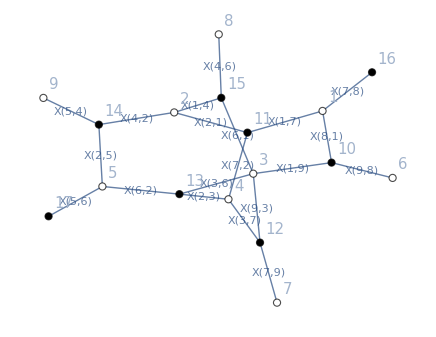

```mathematica
drawBFT[a,b,c,d]
```

```mathematica
pmref=X[1,9] X[2,1] X[2,3] X[2,5] X[4,6] X[7,8] X[7,9];
order={17,9,8,7,6,16};
boundaries={{17,9,8},{7,6,16}};
boundarycuts={{1,2}->{X[3,7]->-X[3,7],X[3,6]->-X[3,6]}};
```

```mathematica
pathmatrix[a,b,c,d,pmref,order]
Print["This is the path matrix 'pathmat':"];
Print[pathmat//MatrixForm];
sources=findSources[a,b,c,d,order,pmref];
sinks=findSinks[a,b,c,d,order,pmref];

(*Now make it nicer and plug in Postnikov's signs*)
(*First make the replacement lists.*)
therule=MapThread[Rule,{plist,Table[Subscript[pp, i],{i,Length[plist]}]}];(*To recognize stuff as perfect matchings*)
inverserule=MapThread[Rule,{Table[Subscript[pp, i],{i,Length[plist]}],plist/pmref}];
repl=MapThread[Rule,{Xlist,ConstantArray[1,Length[Xlist]]}];(*This is needed to get the signs right*)
(*This is for Postnikov's signs*)
newnumberrule=MapThread[Rule,{order,Range[Length[order]]}];
newsource=sources/.newnumberrule;
(*Make the rule for the replacement of loops with variables Subscript[loop, i]*)
looprep={};
invlooprep={};
loopflip={};
looplist=MapThread[Times,{(MonomialList[Expand[loops pmref]]/pmref)/.repl,MonomialList[Expand[loops pmref]]/pmref}];
dummy=1;
For[i=1,i<Length[looplist]+1,i++,
If[looplist[[i]]==1,True,True,
Subscript[l, dummy]=looplist[[i]];
looprep=Join[looprep,{Subscript[l, dummy]->Subscript[loop, dummy]}];
invlooprep=Join[invlooprep,{Subscript[loop, dummy]->Subscript[l, dummy]}];
loopflip=Join[loopflip,{Subscript[loop, dummy]->-Subscript[loop, dummy]}];
dummy=dummy+1;
];
];

postnikovpath=pathmat;(*this will be the path matrix with postnikov's signs incorporated*)
For[i=1,i<Length[sources]+1,i++,(*Rows of the sign matrix*)
For[j=1,j<Length[order]+1,j++,(*Columns of the sign matrix*)
(*This is to get Postnikov's signs*)
count=0;
For[k=1,k<Length[sources]+1,k++,
If[Min[newsource[[i]],j]<newsource[[k]]&&newsource[[k]]<Max[newsource[[i]],j],count=count+1;];
];
(*This is to make it look nice, and plug in the overall signs.*)
If[pathmat[[i,j]]==1||pathmat[[i,j]]==0,True,True,
If[Denominator[pathmat[[i,j]]]==1,
(*we have multiple terms*)
terms={};
For[k=1,k<Length[pathmat[[i,j]]]+1,k++,
If[Length[MonomialList[Denominator[pathmat[[i,j]][[k]]]]]>1,
(*If we have loops*)
terms=Join[terms,{Expand[Simplify[pathmat[[i,j]][[k]]loops]]/loops}];
,terms=Join[terms,{pathmat[[i,j]][[k]]}];(*If we don't have loops*)
];
];
postnikovpath[[i,j]]=Total[terms](-1)^count;
,True,(*we have only one term*)
If[Length[MonomialList[Denominator[pathmat[[i,j]]]]]>1,
(*If the term has loops*)
postnikovpath[[i,j]]=(-1)^count Expand[Simplify[pathmat[[i,j]]loops]]/loops;
,postnikovpath[[i,j]]=(-1)^count pathmat[[i,j]];
];
];
];
(*Done looking nice, and overall signs!*)
];
];
postnikovpathloop=postnikovpath;
(*Now replace loops in postnikovpathloop with Subscript[loop, i] variables*)
change=1;(*Keeps track of whether postnikovpathloop changed when we gave it loopreplacements*)
compa=postnikovpathloop;(*This is what we compare with*)
While[change==1,
postnikovpathloop=postnikovpathloop/.looprep;
If[compa==postnikovpathloop,(*if putting in loop replacement changed nothing, we've replaced all the loops that can be replaced*)
change=0;
];
compa=postnikovpathloop;
];
postnikovpathloop=postnikovpathloop/.loopflip;
postnikovpath=postnikovpathloop/.invlooprep;
Print["Path matrix with Postnikov's overall signs, and signs for loops 'postnikovpath':"];
Print[postnikovpath//MatrixForm];
(*Print[postnikovpathloop//MatrixForm];*)

(*Now plug  in Gekhtman's signs*)
numtoorder=MapThread[Rule,{order,Range[Length[order]]}];
postgekhtmatrixloop=postnikovpathloop;
For[i=1,i<Length[sources]+1,i++,(*Rows of the matrix*)
For[j=1,j<Length[order]+1,j++,(*Columns of the matrix*)
If[postnikovpathloop[[i,j]]==1||postnikovpathloop[[i,j]]==0,True,True,
bguys={};
(*Now find out which boundaries this entries goes between.*)
For[k=1,k<Length[boundaries]+1,k++,
If[MemberQ[boundaries[[k]],sources[[i]]]||MemberQ[boundaries[[k]],order[[j]]],
bguys=Join[bguys,{k}];
];
];
bguys=Sort[bguys];
(*If[i==1&&(j==5||j==4),Print["bguys=",bguys];];*)
If[Length[bguys]==2,(*Only do it if we re going between different boundaries*)
postgekhtmatrixloop[[i,j]]=postnikovpathloop[[i,j]]/.(bguys/.boundarycuts);
];
];
];
];
postgekhtmatrix=postgekhtmatrixloop/.invlooprep;
Print["This is the matrix with also include Gekhtmans's signs 'postgekhtmatrix':"];
Print[postgekhtmatrix//MatrixForm];

(*Now write it up nicely in terms of pms.*)
tempmat=Expand[Simplify[postgekhtmatrix]];
pmpostgekhtmatrix=postgekhtmatrix;
pmloops=((Total[looplist pmref]/.therule)/.{Subscript[pp, Position[plist,pmref][[1,1]]]->1});
For[i=1,i<Length[sources]+1,i++,(*Rows of the sign matrix*)
For[j=1,j<Length[order]+1,j++,(*Columns of the sign matrix*)
If[tempmat[[i,j]]==1||tempmat[[i,j]]==0,True,True,
If[Denominator[tempmat[[i,j]]]==1,
(*we have multiple terms*)
terms={};
For[k=1,k<Length[tempmat[[i,j]]]+1,k++,
If[Length[MonomialList[Denominator[tempmat[[i,j]][[k]]]]]>1,
(*If we have loops*)
terms=Join[terms,{((Expand[Simplify[tempmat[[i,j]][[k]]Total[looplist]]]pmref)/.therule)/pmloops}];
,terms=Join[terms,{((tempmat[[i,j]][[k]]pmref)/.therule)}];(*If we don't have loops*)
];
];
pmpostgekhtmatrix[[i,j]]=Total[terms];
,True,(*we have only one term*)
If[Length[MonomialList[Denominator[tempmat[[i,j]]]]]>1,
(*If the term has loops*)
pmpostgekhtmatrix[[i,j]]=((Expand[Simplify[tempmat[[i,j]]Total[looplist]]] pmref)/.therule)/pmloops;
,pmpostgekhtmatrix[[i,j]]=((tempmat[[i,j]] pmref)/.therule);
];
];
];
(*Done looking nice, and overall signs!*)
];
];
Print["The Grassmannian matrix in terms of perfect matchings is 'pmpostgekhtmatrix':"];
Print[pmpostgekhtmatrix//MatrixForm];

(*Now calculate the Pluckers!*)
plucker=Expand[Simplify[Minors[postgekhtmatrix,Length[sources]][[1]]]];
Print["These are the Pluckers 'plucker':"];
Print[plucker//MatrixForm];

(*Now make the Pluckers look nice*)
niceplucker=plucker;
For[i=1,i<Length[plucker]+1,i++,(*Rows of the sign matrix*)
If[plucker[[i]]==1,True,True,
If[Denominator[plucker[[i]]]==1,
(*we have multiple terms*)
terms={};
For[k=1,k<Length[plucker[[i]]]+1,k++,
If[Length[MonomialList[Denominator[plucker[[i]][[k]]]]]>1,
(*If we have loops*)
terms=Join[terms,{((Expand[Simplify[plucker[[i]][[k]]Total[looplist]]]pmref)/.therule)/pmloops}];
,terms=Join[terms,{((plucker[[i]][[k]]pmref)/.therule)}];(*If we don't have loops*)
];
];
niceplucker[[i]]=Total[terms];
,True,(*we have only one term*)
If[Length[MonomialList[Denominator[plucker[[i]]]]]>1,
(*If the term has loops*)
niceplucker[[i]]=((Expand[Simplify[plucker[[i]]Total[looplist]]] pmref)/.therule)/pmloops;
,niceplucker[[i]]=((plucker[[i]] pmref)/.therule);
];
];
];
(*Done looking nice, and overall signs!*)
];
Print["Pluckers written in terms of perfect matchings 'niceplucker':"];
Print[niceplucker//MatrixForm];
realplucker=Expand[Simplify[plucker Total[looplist]pmref]]/.therule;
Print["Real map between Pluckers and perfect matchings 'realplucker':"];
Print[realplucker//MatrixForm];

(*Now check that the Pluckers are correct, i.e. that they all have the correct source set.*)
kmat=Join[Join[a,c],Join[b,d],2];
btra=Transpose[b];
xtonum={};
For[i=1,i<Length[c]+1,i++,
xtonum=Join[xtonum,{(i+Length[a])->DeleteCases[c[[i]],0][[1]]}];
];
For[j=1,j<Length[btra]+1,j++,
xtonum=Join[xtonum,{(j+Length[a]+Length[c]+Dimensions[a][[2]])->DeleteCases[btra[[j]],0][[1]]}];
];
xorder=order/.xtonum;
ordering=MapThread[Rule,{xorder,Range[Length[order]]}];
(*Done with the first part! Now check source sets...*)
subs=Subsets[Range[Length[order]],{Length[sources]}];
compare={};
For[i=1,i<Length[realplucker]+1,i++,
guys=MapThread[Times,{MonomialList[realplucker[[i]]]/.Table[Subscript[pp, x]->1,{x,Length[plist]}],MonomialList[realplucker[[i]]]}];
For[j=1,j<Length[guys]+1,j++,
compare=Join[compare,{guys[[j]][[2]]->subs[[i]]}];
];
];
compare=Sort[compare];
If[compare==pmsourcesOrderingByHand[a,b,c,d,ordering],
Print["Checked that the source set for these perfect matchings is indeed the Plucker coordiate in question, OK!"];
,Print["It seems like the source set of some of these perfect matchings is NOT the correct Plucker coordinate...CHECK IT!"];
];
```

The full path matrix is 'fullmatrix', the part that goes from sources to sinks is 'pathmat', the loop denominator is 'loops'.

This is the path matrix 'pathmat':

((X[2,1] X[2,3] X[5,4] X[5,6])/(X[2,1] X[2,3] X[2,5]-X[4,2] X[6,2] X[7,2]) | 1 | (X[1,4] X[5,4] X[6,2] X[7,2])/(X[4,6] (X[2,1] X[2,3] X[2,5]-X[4,2] X[6,2] X[7,2])) | (X[2,1] X[3,7] X[5,4] X[6,2])/((X[2,1] X[2,3] X[2,5]-X[4,2] X[6,2] X[7,2]) X[7,9]) | 0 | 0
(X[3,6] X[4,2] X[5,6] X[7,2] X[9,8])/(X[1,9] (X[2,1] X[2,3] X[2,5]-X[4,2] X[6,2] X[7,2])) | 0 | (X[2,1] X[2,3] X[2,5] X[6,1] X[9,8])/(X[1,9] X[4,6] (X[2,1] X[2,3] X[2,5]-X[4,2] X[6,2] X[7,2]))+(X[1,4] X[2,5] X[3,6] X[7,2] X[9,8])/(X[1,9] X[4,6] (X[2,1] X[2,3] X[2,5]-X[4,2] X[6,2] X[7,2]))-(X[4,2] X[6,1] X[6,2] X[7,2] X[9,8])/(X[1,9] X[4,6] (X[2,1] X[2,3] X[2,5]-X[4,2] X[6,2] X[7,2])) | (X[2,1] X[2,5] X[3,6] X[3,7] X[9,8])/(X[1,9] (X[2,1] X[2,3] X[2,5]-X[4,2] X[6,2] X[7,2]) X[7,9])+(X[2,1] X[2,3] X[2,5] X[9,3] X[9,8])/(X[1,9] (X[2,1] X[2,3] X[2,5]-X[4,2] X[6,2] X[7,2]) X[7,9])-(X[4,2] X[6,2] X[7,2] X[9,3] X[9,8])/(X[1,9] (X[2,1] X[2,3] X[2,5]-X[4,2] X[6,2] X[7,2]) X[7,9]) | 1 | 0
(X[1,7] X[2,3] X[4,2] X[5,6])/((X[2,1] X[2,3] X[2,5]-X[4,2] X[6,2] X[7,2]) X[7,8])+(X[3,6] X[4,2] X[5,6] X[7,2] X[8,1])/(X[1,9] (X[2,1] X[2,3] X[2,5]-X[4,2] X[6,2] X[7,2]) X[7,8]) | 0 | (X[1,4] X[1,7] X[2,3] X[2,5])/(X[4,6] (X[2,1] X[2,3] X[2,5]-X[4,2] X[6,2] X[7,2]) X[7,8])+(X[2,1] X[2,3] X[2,5] X[6,1] X[8,1])/(X[1,9] X[4,6] (X[2,1] X[2,3] X[2,5]-X[4,2] X[6,2] X[7,2]) X[7,8])+(X[1,4] X[2,5] X[3,6] X[7,2] X[8,1])/(X[1,9] X[4,6] (X[2,1] X[2,3] X[2,5]-X[4,2] X[6,2] X[7,2]) X[7,8])-(X[4,2] X[6,1] X[6,2] X[7,2] X[8,1])/(X[1,9] X[4,6] (X[2,1] X[2,3] X[2,5]-X[4,2] X[6,2] X[7,2]) X[7,8]) | (X[1,7] X[3,7] X[4,2] X[6,2])/((X[2,1] X[2,3] X[2,5]-X[4,2] X[6,2] X[7,2]) X[7,8] X[7,9])+(X[2,1] X[2,5] X[3,6] X[3,7] X[8,1])/(X[1,9] (X[2,1] X[2,3] X[2,5]-X[4,2] X[6,2] X[7,2]) X[7,8] X[7,9])+(X[2,1] X[2,3] X[2,5] X[8,1] X[9,3])/(X[1,9] (X[2,1] X[2,3] X[2,5]-X[4,2] X[6,2] X[7,2]) X[7,8] X[7,9])-(X[4,2] X[6,2] X[7,2] X[8,1] X[9,3])/(X[1,9] (X[2,1] X[2,3] X[2,5]-X[4,2] X[6,2] X[7,2]) X[7,8] X[7,9]) | 0 | 1)

Path matrix with Postnikov's overall signs, and signs for loops 'postnikovpath':

((X[5,4] X[5,6])/(X[2,5] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5]))) | 1 | (X[1,4] X[5,4] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5] X[4,6] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5]))) | (X[3,7] X[5,4] X[6,2])/(X[2,3] X[2,5] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,9]) | 0 | 0
-(X[3,6] X[4,2] X[5,6] X[7,2] X[9,8])/(X[1,9] X[2,1] X[2,3] X[2,5] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5]))) | 0 | (X[6,1] X[9,8])/(X[1,9] X[4,6] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])))+(X[1,4] X[3,6] X[7,2] X[9,8])/(X[1,9] X[2,1] X[2,3] X[4,6] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])))+(X[4,2] X[6,1] X[6,2] X[7,2] X[9,8])/(X[1,9] X[2,1] X[2,3] X[2,5] X[4,6] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5]))) | (X[3,6] X[3,7] X[9,8])/(X[1,9] X[2,3] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,9])+(X[9,3] X[9,8])/(X[1,9] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,9])+(X[4,2] X[6,2] X[7,2] X[9,3] X[9,8])/(X[1,9] X[2,1] X[2,3] X[2,5] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,9]) | 1 | 0
(X[1,7] X[4,2] X[5,6])/(X[2,1] X[2,5] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,8])+(X[3,6] X[4,2] X[5,6] X[7,2] X[8,1])/(X[1,9] X[2,1] X[2,3] X[2,5] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,8]) | 0 | -(X[1,4] X[1,7])/(X[2,1] X[4,6] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,8])-(X[6,1] X[8,1])/(X[1,9] X[4,6] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,8])-(X[1,4] X[3,6] X[7,2] X[8,1])/(X[1,9] X[2,1] X[2,3] X[4,6] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,8])-(X[4,2] X[6,1] X[6,2] X[7,2] X[8,1])/(X[1,9] X[2,1] X[2,3] X[2,5] X[4,6] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,8]) | -(X[1,7] X[3,7] X[4,2] X[6,2])/(X[2,1] X[2,3] X[2,5] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,8] X[7,9])-(X[3,6] X[3,7] X[8,1])/(X[1,9] X[2,3] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,8] X[7,9])-(X[8,1] X[9,3])/(X[1,9] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,8] X[7,9])-(X[4,2] X[6,2] X[7,2] X[8,1] X[9,3])/(X[1,9] X[2,1] X[2,3] X[2,5] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,8] X[7,9]) | 0 | 1)

This is the matrix with also include Gekhtmans's signs 'postgekhtmatrix':

((X[5,4] X[5,6])/(X[2,5] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5]))) | 1 | (X[1,4] X[5,4] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5] X[4,6] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5]))) | -(X[3,7] X[5,4] X[6,2])/(X[2,3] X[2,5] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,9]) | 0 | 0
(X[3,6] X[4,2] X[5,6] X[7,2] X[9,8])/(X[1,9] X[2,1] X[2,3] X[2,5] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5]))) | 0 | (X[6,1] X[9,8])/(X[1,9] X[4,6] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])))-(X[1,4] X[3,6] X[7,2] X[9,8])/(X[1,9] X[2,1] X[2,3] X[4,6] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])))+(X[4,2] X[6,1] X[6,2] X[7,2] X[9,8])/(X[1,9] X[2,1] X[2,3] X[2,5] X[4,6] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5]))) | (X[3,6] X[3,7] X[9,8])/(X[1,9] X[2,3] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,9])+(X[9,3] X[9,8])/(X[1,9] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,9])+(X[4,2] X[6,2] X[7,2] X[9,3] X[9,8])/(X[1,9] X[2,1] X[2,3] X[2,5] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,9]) | 1 | 0
(X[1,7] X[4,2] X[5,6])/(X[2,1] X[2,5] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,8])-(X[3,6] X[4,2] X[5,6] X[7,2] X[8,1])/(X[1,9] X[2,1] X[2,3] X[2,5] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,8]) | 0 | -(X[1,4] X[1,7])/(X[2,1] X[4,6] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,8])-(X[6,1] X[8,1])/(X[1,9] X[4,6] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,8])+(X[1,4] X[3,6] X[7,2] X[8,1])/(X[1,9] X[2,1] X[2,3] X[4,6] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,8])-(X[4,2] X[6,1] X[6,2] X[7,2] X[8,1])/(X[1,9] X[2,1] X[2,3] X[2,5] X[4,6] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,8]) | -(X[1,7] X[3,7] X[4,2] X[6,2])/(X[2,1] X[2,3] X[2,5] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,8] X[7,9])-(X[3,6] X[3,7] X[8,1])/(X[1,9] X[2,3] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,8] X[7,9])-(X[8,1] X[9,3])/(X[1,9] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,8] X[7,9])-(X[4,2] X[6,2] X[7,2] X[8,1] X[9,3])/(X[1,9] X[2,1] X[2,3] X[2,5] (1+(X[4,2] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5])) X[7,8] X[7,9]) | 0 | 1)

The Grassmannian matrix in terms of perfect matchings is 'pmpostgekhtmatrix':

(pp_2/(1+pp_6) | 1 | pp_8/(1+pp_6) | -pp_1/(1+pp_6) | 0 | 0
pp_31/(1+pp_6) | 0 | pp_23/(1+pp_6)+pp_39/(1+pp_6)-pp_41/(1+pp_6) | pp_13/(1+pp_6)+pp_19/(1+pp_6)+pp_29/(1+pp_6) | 1 | 0
pp_7/(1+pp_6)-pp_33/(1+pp_6) | 0 | -pp_10/(1+pp_6)-pp_24/(1+pp_6)-pp_40/(1+pp_6)+pp_44/(1+pp_6) | -pp_4/(1+pp_6)-pp_14/(1+pp_6)-pp_20/(1+pp_6)-pp_30/(1+pp_6) | 0 | 1)

These are the Pluckers 'plucker':

((X[1,7] X[2,3] X[4,2] X[5,6] X[6,1] X[9,8])/(X[1,9] X[2,1] X[2,3] X[2,5] X[4,6] X[7,8]+X[1,9] X[4,2] X[4,6] X[6,2] X[7,2] X[7,8])
(X[1,7] X[3,6] X[3,7] X[4,2] X[5,6] X[9,8])/(X[1,9] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,8] X[7,9])+(X[1,7] X[2,3] X[4,2] X[5,6] X[9,3] X[9,8])/(X[1,9] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,8] X[7,9])
(X[1,7] X[2,3] X[4,2] X[5,6])/((X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,8])-(X[3,6] X[4,2] X[5,6] X[7,2] X[8,1])/(X[1,9] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,8])
-(X[3,6] X[4,2] X[5,6] X[7,2] X[9,8])/(X[1,9] X[2,1] X[2,3] X[2,5]+X[1,9] X[4,2] X[6,2] X[7,2])
(X[1,4] X[1,7] X[3,6] X[3,7] X[5,4] X[5,6] X[9,8])/(X[1,9] X[4,6] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,8] X[7,9])+(X[1,4] X[1,7] X[2,3] X[5,4] X[5,6] X[9,3] X[9,8])/(X[1,9] X[4,6] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,8] X[7,9])
(X[1,4] X[1,7] X[2,3] X[5,4] X[5,6])/(X[4,6] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,8])+(X[2,1] X[2,3] X[5,4] X[5,6] X[6,1] X[8,1])/(X[1,9] X[4,6] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,8])-(X[1,4] X[3,6] X[5,4] X[5,6] X[7,2] X[8,1])/(X[1,9] X[4,6] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,8])
(X[2,1] X[2,3] X[5,4] X[5,6] X[6,1] X[9,8])/(X[1,9] X[4,6] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]))-(X[1,4] X[3,6] X[5,4] X[5,6] X[7,2] X[9,8])/(X[1,9] X[4,6] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]))
(X[2,1] X[3,6] X[3,7] X[5,4] X[5,6] X[8,1])/(X[1,9] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,8] X[7,9])+(X[2,1] X[2,3] X[5,4] X[5,6] X[8,1] X[9,3])/(X[1,9] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,8] X[7,9])
(X[2,1] X[3,6] X[3,7] X[5,4] X[5,6] X[9,8])/(X[1,9] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,9])+(X[2,1] X[2,3] X[5,4] X[5,6] X[9,3] X[9,8])/(X[1,9] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,9])
(X[2,1] X[2,3] X[5,4] X[5,6])/(X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2])
(X[1,4] X[1,7] X[2,5] X[3,6] X[3,7] X[9,8])/(X[1,9] X[4,6] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,8] X[7,9])-(X[1,7] X[3,7] X[4,2] X[6,1] X[6,2] X[9,8])/(X[1,9] X[4,6] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,8] X[7,9])+(X[1,4] X[1,7] X[2,3] X[2,5] X[9,3] X[9,8])/(X[1,9] X[4,6] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,8] X[7,9])
(X[1,4] X[1,7] X[2,3] X[2,5])/(X[4,6] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,8])+(X[2,1] X[2,3] X[2,5] X[6,1] X[8,1])/(X[1,9] X[4,6] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,8])-(X[1,4] X[2,5] X[3,6] X[7,2] X[8,1])/(X[1,9] X[4,6] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,8])+(X[4,2] X[6,1] X[6,2] X[7,2] X[8,1])/(X[1,9] X[4,6] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,8])
(X[2,1] X[2,3] X[2,5] X[6,1] X[9,8])/(X[1,9] X[4,6] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]))-(X[1,4] X[2,5] X[3,6] X[7,2] X[9,8])/(X[1,9] X[4,6] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]))+(X[4,2] X[6,1] X[6,2] X[7,2] X[9,8])/(X[1,9] X[4,6] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]))
(X[1,7] X[3,7] X[4,2] X[6,2])/((X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,8] X[7,9])+(X[2,1] X[2,5] X[3,6] X[3,7] X[8,1])/(X[1,9] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,8] X[7,9])+(X[2,1] X[2,3] X[2,5] X[8,1] X[9,3])/(X[1,9] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,8] X[7,9])+(X[4,2] X[6,2] X[7,2] X[8,1] X[9,3])/(X[1,9] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,8] X[7,9])
(X[2,1] X[2,5] X[3,6] X[3,7] X[9,8])/(X[1,9] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,9])+(X[2,1] X[2,3] X[2,5] X[9,3] X[9,8])/(X[1,9] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,9])+(X[4,2] X[6,2] X[7,2] X[9,3] X[9,8])/(X[1,9] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,9])
1
(X[1,4] X[1,7] X[3,7] X[5,4] X[6,2])/(X[4,6] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,8] X[7,9])+(X[2,1] X[3,7] X[5,4] X[6,1] X[6,2] X[8,1])/(X[1,9] X[4,6] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,8] X[7,9])+(X[1,4] X[5,4] X[6,2] X[7,2] X[8,1] X[9,3])/(X[1,9] X[4,6] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,8] X[7,9])
(X[2,1] X[3,7] X[5,4] X[6,1] X[6,2] X[9,8])/(X[1,9] X[4,6] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,9])+(X[1,4] X[5,4] X[6,2] X[7,2] X[9,3] X[9,8])/(X[1,9] X[4,6] (X[2,1] X[2,3] X[2,5]+X[4,2] X[6,2] X[7,2]) X[7,9])
(X[1,4] X[5,4] X[6,2] X[7,2])/(X[2,1] X[2,3] X[2,5] X[4,6]+X[4,2] X[4,6] X[6,2] X[7,2])
-(X[2,1] X[3,7] X[5,4] X[6,2])/(X[2,1] X[2,3] X[2,5] X[7,9]+X[4,2] X[6,2] X[7,2] X[7,9]))

Pluckers written in terms of perfect matchings 'niceplucker':

(pp_42/(1+pp_6)
pp_25/(1+pp_6)+pp_32/(1+pp_6)
pp_7/(1+pp_6)-pp_33/(1+pp_6)
-pp_31/(1+pp_6)
pp_26/(1+pp_6)+pp_37/(1+pp_6)
pp_9/(1+pp_6)+pp_22/(1+pp_6)-pp_38/(1+pp_6)
pp_21/(1+pp_6)-pp_36/(1+pp_6)
pp_12/(1+pp_6)+pp_18/(1+pp_6)
pp_11/(1+pp_6)+pp_17/(1+pp_6)
pp_2/(1+pp_6)
-pp_27/(1+pp_6)+pp_28/(1+pp_6)+pp_43/(1+pp_6)
pp_10/(1+pp_6)+pp_24/(1+pp_6)+pp_40/(1+pp_6)-pp_44/(1+pp_6)
pp_23/(1+pp_6)+pp_39/(1+pp_6)-pp_41/(1+pp_6)
pp_4/(1+pp_6)+pp_14/(1+pp_6)+pp_20/(1+pp_6)+pp_30/(1+pp_6)
pp_13/(1+pp_6)+pp_19/(1+pp_6)+pp_29/(1+pp_6)
1
pp_5/(1+pp_6)+pp_16/(1+pp_6)+pp_35/(1+pp_6)
pp_15/(1+pp_6)+pp_34/(1+pp_6)
pp_8/(1+pp_6)
-pp_1/(1+pp_6))

Real map between Pluckers and perfect matchings 'realplucker':

(pp_42
pp_25+pp_32
pp_7-pp_33
-pp_31
pp_26+pp_37
pp_9+pp_22-pp_38
pp_21-pp_36
pp_12+pp_18
pp_11+pp_17
pp_2
-pp_27+pp_28+pp_43
pp_10+pp_24+pp_40-pp_44
pp_23+pp_39-pp_41
pp_4+pp_14+pp_20+pp_30
pp_13+pp_19+pp_29
pp_3+pp_6
pp_5+pp_16+pp_35
pp_15+pp_34
pp_8
-pp_1)

Checked that the source set for these perfect matchings is indeed the Plucker coordiate in question, OK!